## Functions

### Chip Seq Functions

#### Organize Data by Q-value and mapping

```mathematica
(*Annotation of possible headers for chromosome text strings. chrList is the most common annotation and this is converted into numeric entries for sorting*)
```

```mathematica
chrList =Flatten[Append[Table[StringJoin["chr",ToString[i]],{i,1,22}],{"chrX","chrY"}]];
chrList2 =Flatten[Append[Table[StringJoin["Chromosome",ToString[i]],{i,1,22}],{"ChromosomeX","ChromosomeY"}]];
chrList3  =Flatten[Append[Table[i,{i,1,22}],{"X","Y"}]];
m=1000;
syntaxMapNumericChr = Table[chrList[[i]]->i,{i,22}];
syntaxMapNumericChrXY = Table[chrList[[i]]->i,{i,24}];
```

```mathematica
(*Can change #[[24]] such that it's positive by changing to >0 peaks created in ALDH+ cells, or negative peaks lost by <0. Here we take all differential peaks. Similar patterns are seen with formed peaks*)
(*Can change #[[26]] to adjust the p-value of the peaks*)
(*Can change #[[2]] to grab variant chromosome mappings*)
```

```mathematica
orgCondByChromosome[marker_]:=SplitBy[SortBy[Select[marker,(StringLength[#[[2]]]<=5&&#[[24]]!=0&&#[[26]]<.05)&]/.syntaxMapNumericChrXY,#[[2]]&],#[[2]]&];
```

```mathematica
(*Segment length for each peak*)
```

```mathematica
chrChipCounts[mark_]:=Table[Transpose[mark[[i]]][[4]] -Transpose[mark[[i]]][[3]],{i,Length[mark]}];
```

## Analysis of Nucleosome Markers

### Load Data

#### Directory

```mathematica
(*Set your working directory*)
```

```mathematica
dir = SetDirectory@NotebookDirectory[]
```

/Users/lma250/Documents/Research/Backman Lab/Chemoresistance/Ovarian Stem Cell Data/Cut N Tag ChIP-seq data

#### General Organization

```mathematica
(*Mathematica default lengths are Hg19; Manual values entered from NCBI values*)
```

```mathematica
chrsLengths = Table[GenomeData[i,"SequenceLength"],{i,1,24}];
```

```mathematica
chrsLengthsHg38 = {248956422,242193529,198295559,190214555,181538259,170805979,159345973,145138636,138394717,133797422,135086622,133275309,114364328,107043718,101991189,90338345,83257441,80373285,58617616,64444167,46709983,50818468,156040895,57227415};
```

chrsLengthsHg38 was input from https://www.ncbi.nlm.nih.gov/grc/human/data

### CHIP Data

#### ChipSeq Data

```mathematica
(*pLoc is default comparison position*)
```

```mathematica
pLoc=1;
```

```mathematica
(*file locations*)
```

```mathematica
tDone = FileNames["*.txt",StringJoin[dir,"/Differential Peaks/"],2];
markToCheck ={"K4me3","K27ac","K27me3"};
markStrings= Table[Select[tDone, StringContainsQ[StringJoin["/",If[StringQ[markToCheck[[i]]],markToCheck[[i]],ToString[markToCheck[[i]]]]]]],{i,Length[markToCheck]}];
```

```mathematica
(*confirm the file names and locations*)
```

```mathematica
TableForm[markStrings]
```

/Users/lma250/Documents/Research/Backman Lab/Chemoresistance/Ovarian Stem Cell Data/Cut N Tag ChIP-seq data/Differential Peaks/K4me3.homerDiffPeaks.anno.txt
/Users/lma250/Documents/Research/Backman Lab/Chemoresistance/Ovarian Stem Cell Data/Cut N Tag ChIP-seq data/Differential Peaks/K27ac.homerDiffPeaks.anno.txt
/Users/lma250/Documents/Research/Backman Lab/Chemoresistance/Ovarian Stem Cell Data/Cut N Tag ChIP-seq data/Differential Peaks/K27me3.homerDiffPeaks.anno.txt

```mathematica
(*import the data*)
```

```mathematica
markMatrix = Import[#[[1]],"Data"]&/@markStrings;
```

```mathematica
(*organize it so that pvalue <0.05 and ordered by chromosome number*)
```

```mathematica
organizedMarks = Table[orgCondByChromosome[markMatrix[[i]]],{i,Length[markMatrix]}];
```

```mathematica
(*header positions within the raw data*)
```

```mathematica
TableForm[markMatrix[[1,1]]]
```

#cmd=getDifferentialPeaksReplicates.pl -genome hg38 -all -t K4me3.A_plus_R1_tagDir K4me3.A_plus_R2_tagDir -b K4me3.A_minus_R1_tagDir K4me3.A_minus_R2_tagDir -style histone|PeakID (cmd=annotatePeaks.pl 0.311154399606497.peaks hg38 -d K4me3.A_minus_R1_tagDir K4me3.A_minus_R2_tagDir K4me3.A_plus_R1_tagDir K4me3.A_plus_R2_tagDir -raw) (cmd=getDiffExpression.pl 0.311154399606497.raw.txt bg bg target target -norm2total -DESeq2 -fdr 0.05 -log2fold 1 -export 0.311154399606497)
Chr
Start
End
Strand
Peak Score
Focus Ratio/Region Size
Annotation
Detailed Annotation
Distance to TSS
Nearest PromoterID
Entrez ID
Nearest Unigene
Nearest Refseq
Nearest Ensembl
Gene Name
Gene Alias
Gene Description
Gene Type
K4me3.A_minus_R1_tagDir Tag Count in given bp (15715860.0 Total, normalization factor = 1, effective total = 10000000)
K4me3.A_minus_R2_tagDir Tag Count in given bp (21410452.0 Total, normalization factor = 1, effective total = 10000000)
K4me3.A_plus_R1_tagDir Tag Count in given bp (12011954.0 Total, normalization factor = 1, effective total = 10000000)
K4me3.A_plus_R2_tagDir Tag Count in given bp (22777551.0 Total, normalization factor = 1, effective total = 10000000)
bg vs. target Log2 Fold Change
bg vs. target p-value
bg vs. target adj. p-value

```mathematica
(*look at some of the data to make sure it's well organized*)
```

```mathematica
TableForm[organizedMarks[[1,1,1;;10]]]
```

chr1-13752 | 1 | 93771823 | 93775709 | + | 502.5 | 3886 | intron (NR_148965, intron 1 of 1) | intron (NR_148965, intron 1 of 1) | 1617 | NR_148965 | 723788 | Hs.659312 | NR_148965 | ENSG00000137936 | MIG7 | - | mig-7 | ncRNA | 8.98971 | 8.92928 | 9.57178 | 9.51828 | 1.0449 | 2.56×10^-16 | 1.72×10^-13
chr1-14412 | 1 | 245153243 | 245157474 | + | 267 | 4231 | 5' UTR (NM_018012, exon 1 of 15) | 5' UTR (NM_018012, exon 1 of 15) | 373 | NM_018012 | 55083 | Hs.143134 | NM_018012 | ENSG00000162849 | KIF26B | - | kinesin family member 26B | protein-coding | 9.3664 | 9.3167 | 9.07183 | 9.07819 | -0.486195 | 0.000151172 | 0.00533039
chr1-15201 | 1 | 183185767 | 183189232 | + | 199.3 | 3465 | intron (NM_005562, intron 1 of 22) | L1MA9|LINE|L1 | 1235 | NM_018891 | 3918 | Hs.591484 | NM_005562 | ENSG00000058085 | LAMC2 | B2T|BM600|CSF|EBR2|EBR2A|LAMB2T|LAMNB2 | laminin subunit gamma 2 | protein-coding | 8.11475 | 8.02065 | 8.3252 | 8.25266 | 0.500809 | 0.00138603 | 0.0291518
chr1-15297 | 1 | 58573896 | 58579185 | + | 964.8 | 5289 | exon (NM_002353, exon 1 of 1) | exon (NM_002353, exon 1 of 1) | 712 | NM_002353 | 4070 | Hs.23582 | NM_002353 | ENSG00000184292 | TACSTD2 | EGP-1|EGP1|GA733-1|GA7331|GP50|M1S1|TROP2 | tumor associated calcium signal transducer 2 | protein-coding | 10.2887 | 10.0668 | 10.6581 | 10.6172 | 0.639312 | 2.66×10^-8 | 3.79×10^-6
chr1-16514 | 1 | 164558684 | 164562722 | + | 302.4 | 4038 | intron (NM_001353130, intron 1 of 7) | intron (NM_001353130, intron 1 of 7) | 981 | NM_001353130 | 5087 | Hs.557097 | NM_002585 | ENSG00000185630 | PBX1 | CAKUHED | PBX homeobox 1 | protein-coding | 8.70986 | 8.68541 | 9.05586 | 8.8653 | 0.501351 | 0.000621584 | 0.016075
chr1-17039 | 1 | 184036269 | 184038057 | + | 281.6 | 1788 | exon (NM_001303420, exon 1 of 12) | exon (NM_001303420, exon 1 of 12) | 565 | NM_001303420 | 23127 | Hs.387995 | NM_015101 | ENSG00000198756 | COLGALT2 | C1orf17|ColGalT 2|GLT25D2 | collagen beta(1-O)galactosyltransferase 2 | protein-coding | 9.39597 | 9.31241 | 9.06182 | 9.15219 | -0.436806 | 0.000973488 | 0.022788
chr1-17775 | 1 | 205504093 | 205506583 | + | 497.6 | 2490 | intron (NM_002596, intron 1 of 15) | intron (NM_002596, intron 1 of 15) | 669 | NM_002596 | 5129 | Hs.445402 | NM_002596 | ENSG00000117266 | CDK18 | PCTAIRE|PCTAIRE3|PCTK3 | cyclin dependent kinase 18 | protein-coding | 9.39018 | 9.44824 | 9.64152 | 9.7014 | 0.426595 | 0.000433896 | 0.0120771
chr1-18524 | 1 | 5855318 | 5857362 | + | 165.6 | 2044 | Intergenic | Intergenic | 6401 | NR_039838 | 100616421 |  | NR_039838 | ENSG00000264101 | MIR4689 | mir-4689 | microRNA 4689 | ncRNA | 7.8205 | 7.82742 | 8.04503 | 7.98362 | 0.476288 | 0.00271342 | 0.0467577
chr1-18564 | 1 | 111541912 | 111543390 | + | 44 | 1478 | intron (NM_001370216, intron 1 of 7) | intron (NM_001370216, intron 1 of 7) | 642 | NM_001370216 | 5906 | Hs.190334 | NM_002884 | ENSG00000116473 | RAP1A | C21KG|G-22K|KREV-1|KREV1|RAP1|SMGP21 | RAP1A, member of RAS oncogene family | protein-coding | 7.34718 | 7.4063 | 7.14804 | 7.06221 | -0.791477 | 3.06×10^-6 | 0.000228307
chr1-19094 | 1 | 200038729 | 200043377 | + | 750.1 | 4648 | intron (NM_205860, intron 2 of 7) | intron (NM_205860, intron 2 of 7) | -1772 | NM_001276464 | 2494 | Hs.33446 | NM_003822 | ENSG00000116833 | NR5A2 | B1F|B1F2|CPF|FTF|FTZ-F1|FTZ-F1beta|LRH-1|LRH1|hB1F-2 | nuclear receptor subfamily 5 group A member 2 | protein-coding | 9.61592 | 9.8086 | 10.2365 | 10.2116 | 0.761584 | 3.88×10^-10 | 8.15×10^-8

## Analyze ChipSeq Data

### Data Structure and Organization

#### Values distribution for different marks

```mathematica
(*Calculate total segment lengths on each chromosome*)
```

```mathematica
qValueDistribution = Table[Transpose[Flatten[organizedMarks[[i]],1]][[26]],{i,Length[organizedMarks]}];
```

```mathematica
markCoverage = Table[Transpose[
Flatten[organizedMarks[[i]],1]][[4]]-Transpose[
Flatten[organizedMarks[[i]],1]][[3]],{i,Length[organizedMarks]}];
```

```mathematica
markCoverageByChr = Table[chrChipCounts[organizedMarks[[i]]],{i,Length[organizedMarks]}];
```

```mathematica
markTotalsbyChr = Table[N[Total[markCoverageByChr[[i,j]]]],{i,Length[markCoverageByChr]}, {j,Length[markCoverageByChr[[i]]]}];
```

#### Fits Across Chromosomes Levels

```mathematica
(*Output the fractions of each chromosome for a set of marks, pLoc is the default position to compare specified above*)
```

```mathematica
TableForm[{(markTotalsbyChr[[2,1;;22]]/chrsLengthsHg38[[1;;22]]),(markTotalsbyChr[[pLoc,1;;22]]/chrsLengthsHg38[[1;;22]])}]
```

0.010546 | 0.0152355 | 0.00967343 | 0.00495653 | 0.0103962 | 0.00664838 | 0.0149646 | 0.0165013 | 0.00906884 | 0.0092586 | 0.026886 | 0.00979768 | 0.00697134 | 0.0130779 | 0.0203243 | 0.031555 | 0.0335185 | 0.00509083 | 0.032372 | 0.014697 | 0.00537301 | 0.0121553
0.00115605 | 0.000991034 | 0.00110332 | 0.000672593 | 0.00113089 | 0.000923317 | 0.00141484 | 0.00087867 | 0.000648912 | 0.000776457 | 0.00201439 | 0.000964282 | 0.00119522 | 0.00133595 | 0.00255471 | 0.00330769 | 0.00315103 | 0.000365159 | 0.00233595 | 0.00443506 | 0.000708928 | 0.00197188

```mathematica
(*Linear fits*)
```

```mathematica
k4me3k27me3LinearFit = LinearModelFit[Transpose[{Rescale[(markTotalsbyChr[[1,1;;22]]/chrsLengthsHg38[[1;;22]])],Rescale[(markTotalsbyChr[[3,1;;22]]/chrsLengthsHg38[[1;;22]])]}],x,x]
k27ack27me3LinearFit = LinearModelFit[Transpose[{Rescale[(markTotalsbyChr[[2,1;;22]]/chrsLengthsHg38[[1;;22]])],Rescale[(markTotalsbyChr[[3,1;;22]]/chrsLengthsHg38[[1;;22]])]}],x,x]
```

FittedModel[0.083917+0.821165 x]

FittedModel[0.159987+0.485894 x]

```mathematica
k4me3k27acLinearFit = LinearModelFit[Transpose[{Rescale[(markTotalsbyChr[[1,1;;22]]/chrsLengthsHg38[[1;;22]])],Rescale[(markTotalsbyChr[[2,1;;22]]/chrsLengthsHg38[[1;;22]])]}],x,x]
```

FittedModel[0.0840685+0.861443 x]

```mathematica
(*Calculated R-Squared from fits above*)
```

```mathematica
k4me3k27me3LinearFit["RSquared"]
k27ack27me3LinearFit["RSquared"]
k4me3k27acLinearFit["RSquared"]
```

0.781283

0.416483

0.4874

### Visualize Results

```mathematica
(*Plot data vs fits*)
```

#### Relation between marker densities

```mathematica
(*H3K4me3 vs H3K27me3*)
```

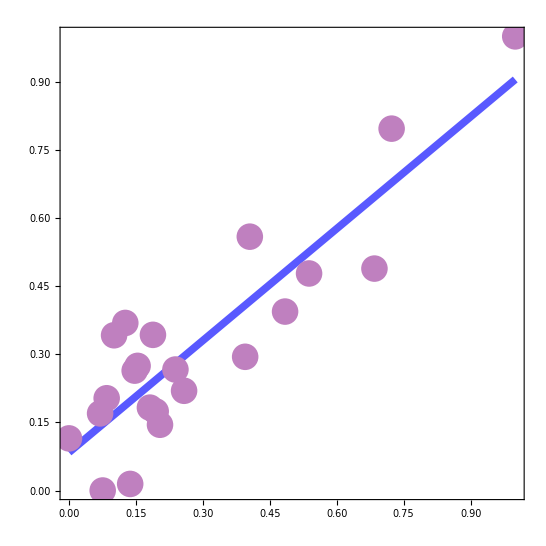

```mathematica
Show[{
Plot[k4me3k27me3LinearFit[x],{x,0,1}, PlotStyle->Directive[Thickness[.01],Lighter[Blue,.35]],AxesOrigin->{0,0}],

ListPlot[
{
Transpose[{Rescale[(markTotalsbyChr[[1,1;;22]]/chrsLengthsHg38[[1;;22]])],Rescale[(markTotalsbyChr[[3,1;;22]]/chrsLengthsHg38[[1;;22]])]}]
},AxesOrigin->{0,0},PlotStyle->{Directive[Lighter[Purple,.5], PointSize[.035]],Directive[Red, PointSize[.035]] }
]},AspectRatio->1, PlotRange->All,AxesStyle->Directive[Black, Bold, 14], Frame-> {{True, False},{True, False}},FrameStyle->Directive[Thickness[.0075],Black,Bold,32]
]
```

```mathematica
(*H3K27ac vs H3K27me3*)
```

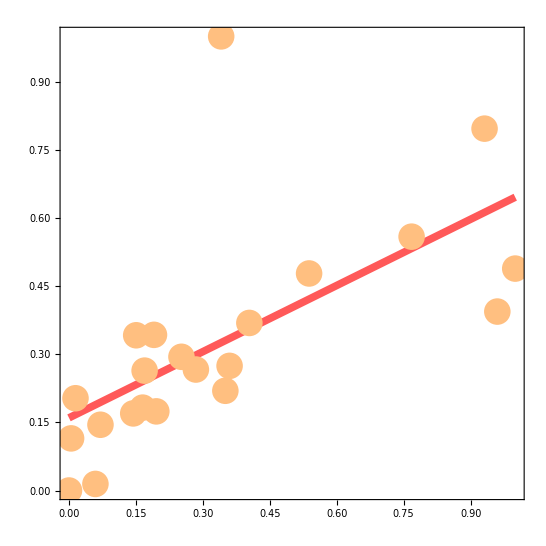

```mathematica
Show[{
Plot[k27ack27me3LinearFit[x],{x,0,1}, PlotStyle->Directive[Thickness[.01],Lighter[Red,.35]],AxesOrigin->{0,0}],

ListPlot[
{
Transpose[{Rescale[(markTotalsbyChr[[2,1;;22]]/chrsLengthsHg38[[1;;22]])],Rescale[(markTotalsbyChr[[3,1;;22]]/chrsLengthsHg38[[1;;22]])]}]
},AxesOrigin->{0,0},PlotStyle->{Directive[Lighter[Orange,.5], PointSize[.035]],Directive[Red, PointSize[.035]] }
]},AspectRatio->1, PlotRange->All,AxesStyle->Directive[Black, Bold, 14], Frame-> {{True, False},{True, False}},FrameStyle->Directive[Thickness[.0075],Black,Bold,32]
]
```

```mathematica
(*H3K4me3 vs H3K27ac*)
```

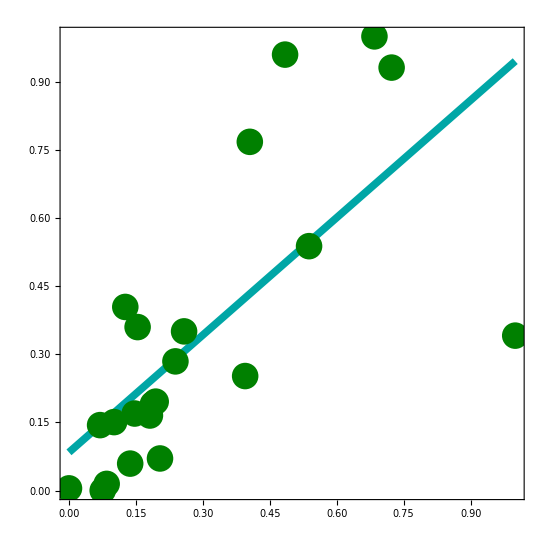

```mathematica
Show[{
Plot[k4me3k27acLinearFit[x],{x,0,1}, PlotStyle->Directive[Thickness[.01],Darker[Cyan,.35]],AxesOrigin->{0,0}],

ListPlot[
{
Transpose[{Rescale[(markTotalsbyChr[[1,1;;22]]/chrsLengthsHg38[[1;;22]])],Rescale[(markTotalsbyChr[[2,1;;22]]/chrsLengthsHg38[[1;;22]])]}]
},AxesOrigin->{0,0},PlotStyle->{Directive[Darker[Green,.5], PointSize[.035]],Directive[Red, PointSize[.035]] }
]},AspectRatio->1, PlotRange->All,AxesStyle->Directive[Black, Bold, 14], Frame-> {{True, False},{True, False}},FrameStyle->Directive[Thickness[.0075],Black,Bold,32]
]
```